Storing Things

The Wolfram Language makes it easy to store things either in the Wolfram Cloud, or locally on your computer system. Let’s talk about the Wolfram Cloud first.

In the Wolfram Cloud everything is a cloud object, specified by a UUID (universally unique identifier).

Cloud objects are immediately assigned a UUID:

```mathematica
CloudObject[ ]
```

CloudObject[]

As soon as you create a cloud object, it’s assigned a long randomly generated UUID. The great thing about UUIDs is that one can assume that there’ll never be two of the same generated. (There are 300 trillion trillion trillion possible Wolfram UUIDs.)

Put a Wolfram Language expression into the cloud:

```mathematica
CloudPut[{-Graphics-,-Graphics-}]
```

CloudObject[]

Get the expression back from the cloud:

```mathematica
CloudGet[%]
```

{-Graphics-,-Graphics-}

If you’ve made definitions using = and :=, you can save these using CloudSave. (If your definitions depend on other definitions, these will get saved too.) You can load your definitions into a new session using CloudGet.

Make a definition:

```mathematica
colorlist[n_Integer]:=RandomColor[n]
```

Save it in the cloud to be retrieved later using CloudGet:

```mathematica
CloudSave[colorlist]
```

CloudObject[]

CloudPut lets you store single Wolfram Language expressions. But what if you want to progressively accumulate expressions—coming either from within the Wolfram Language, or, say, from an outside device or sensor?

The Wolfram Data Drop lets you do exactly this. You start by creating a databin. You can do this in the Wolfram Language using CreateDatabin.

Create a databin:

```mathematica
bin=CreateDatabin[ ]
```

Databin[…]

You can add data to this databin from all sorts of outside devices and services—as well as using the DatabinAdd function in the Wolfram Language.

Add an entry to a databin:

```mathematica
DatabinAdd[bin,{1,2,3,4}]
```

Databin[…]

Add another entry to the same databin:

```mathematica
DatabinAdd[bin,{a,b,c}]
```

Databin[]

Get the values stored in the databin:

```mathematica
Values[bin]
```

{{1,2,3,4},{a,b,c}}

Here’s a databin that’s accumulated data from a little sensor on my desk. DateListPlot plots the time series of data.

Use a short ID to reference a databin connected to sensors on my desk:

```mathematica
Databin["7m3ujLVf"]
```

Databin[…]

Plot time series from the databin:

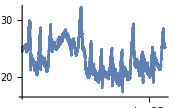
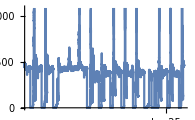
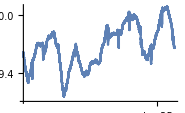
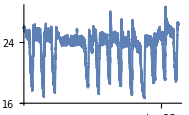
<|humidity→-Graphics-,light→-Graphics-,pressure→-Graphics-,temperature→-Graphics-|>

```mathematica
ListLinePlot[Databin["7m3ujLVf"]]
```

Wolfram Data Drop, like CloudPut and CloudSave, saves data into the cloud. But particularly if you’re not connected to the cloud, you may instead want to store things on a local computer. If you figure out where in your filesystem you want the files to go, you can use Put, Save and Get to store and retrieve them.

It’s also possible to get the Wolfram Language to automatically figure out an “anonymous” local location. You can do this with LocalObject.

Generate an “anonymous” location for Put, Save, etc.:

```mathematica
LocalObject[ ]
```

LocalObject[file:///Users/sw/Library/Wolfram/Objects/365e034d-9830-4842-8681-75d3714b3d19]

Put an image to the location:

```mathematica
Put[-Graphics-,%]
```

LocalObject[file:///Users/sw/Library/Wolfram/Objects/365e034d-9830-4842-8681-75d3714b3d19]

Get the image back:

```mathematica
Get[%]
```

-Graphics-

Vocabulary

CloudObject[ ] |   | create a cloud object
CloudPut[expr] |   | put into the cloud
CloudGet[obj] |   | get from the cloud 
CloudSave[s] |   | save definitions to the cloud
Databin["id"] |   | a databin with accumulated data
CreateDatabin[ ] |   | create a new databin
DatabinAdd[obj,value] |   | add something to a databin
DateListPlot[data] |   | make a date list plot
LocalObject[ ] |   | create a local object
Put[expr,obj] |   | put into a local object
Get[obj] |   | get from a local object

Q&A

What do the letters and numbers in UUIDs mean?

They’re digits in hexadecimal (base 16); the letters “a” through “f” are the hex digits 10 through 15. Each UUID has 32 hex digits, corresponding to 16^32≈3×10^38 possibilities.

How does the number of possible UUIDs compare to other things?

It’s about the number of atoms in a cubic kilometer of water, or 100 trillion times the number of stars in the universe. If every one of 50 billion computers on Earth generated a UUID at 10 GHz, it’d take the age of the universe to run out of UUIDs.

How do UUIDs relate to short IDs?

All short IDs as generated by URLShorten are explicitly registered, and guaranteed to be unique, a bit like domain names on the internet. UUIDs are long enough that they can be assumed to be unique, even without any kind of central registration.

Can I specify a file name in CloudObject, CloudPut, etc.?

Yes. And the file name will be taken to be relative to your home directory in the cloud. The file will also get a URL, that includes the base of the cloud you’re using, and your user ID.

Can other people access what I store in a cloud object?

Not usually. But if you set the option Permissions→"Public" then everyone can access it, just like we discussed for web apps in Section 36. You can also define exactly who you want to allow to do what with it.

Can I work with databins without using the Wolfram Language?

Yes. You can use the web and many other systems to create and add to databins.

Is there a way to manipulate an expression in the cloud, without getting the whole expression?

Yes. Make it a cloud expression (using CreateCloudExpression). Then all the usual ways of getting and setting parts of the expression will work, but the expression will be persistently stored in the cloud.

How can I save function definitions?

You can put them in a file using Save or in the cloud using CloudSave. You can also use CreateNotebook["FunctionResource"] to create a definition notebook that lets you publish definitions so you or others can use them anywhere through ResourceFunction[...].

Tech Notes

When you work in the cloud, Wolfram Notebook documents are automatically stored after every change you make—unless you say not to do this.

You can save large objects more efficiently with DumpSave than Save, but then the file you create is binary, not text.

LocalCache[CloudObject[...]] is a way to refer to a cloud object, but to use a local cache of its contents if that’s available (and create it if it’s not).

Databins can have data signatures, that specify how data in them should be interpreted, for example in terms of units, date formats, etc.

An assignment like x=3 lasts only for the duration of a Wolfram Language session. But you can use things like PersistentSymbol["x"]=3 to store values with different degrees of persistence (on a single computer; whenever you log in; for a certain time; etc.)

The Resource System provides a centralized mechanism for publishing definitions for private or public use. Functions like ResourceFunction and ResourceData let you access such definitions anywhere.

More to Explore

Guide to Files in the Wolfram Language »

Wolfram Data Drop »